```mathematica
ClearAll;

Off[LinearSolve::luc]
Off[$RecursionLimit::reclim2]
colo=ColorData[3,"ColorList"][[{6,2,4}]]
```

{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]}

1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
HC=197.32858;
MUL=1;
pi="-";

v18uixpath="/home/kirscher/kette_repo/ComptonLIT/v18uix_helium3/";
litpath3He="/home/kirscher/kette_repo/ComptonLIT/mul_helion/";

LIThamDET[hh_,nn_,σr_,σi_,B0_]:=Det[hh-(B0+σr+I σi) nn];
LIThamEV[hh_,nn_,σr_,σi_,B0_]:=Eigenvalues[hh-(B0+σr+I σi) nn];

LofM[jjJ_,mmJ_,sR_,sI_,kk_]:=Module[{mJ=mmJ,jJ=jjJ,sigmaRange=sR,sigmaI=sI},

file=v18uixpath<>"norm-ham-litME-"<>ToString[jJ]<>"^"<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file=v18uixpath<>"LIT_SOURCE_"<>ToString[jJ]<>"^"<>pi<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
Dimensions[norm];Dimensions[ham];
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[kk]];
litOfSigma={};
psilitOfSigma={};
For[n=1,n<=nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
psilitOfSigma=Append[psilitOfSigma,coeff];
(* the prefactor (-)^(I_i-I_f+L-L'+nu') is +1 in this (I_i=I_f, L=L', nu=nu'="electric"=0) case *)
litOfSigma=Append[litOfSigma,Conjugate[coeff].norm.coeff];
)];

{litOfSigma,norm,ham,psilitOfSigma}
]
```

Setup of the RHS of the LIT equation  (Η̂-B_(3-helium)-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_(3-helium)]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_(3-helium)-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_(3-helium)]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

ω=1.02MeV

ω=2.02MeV

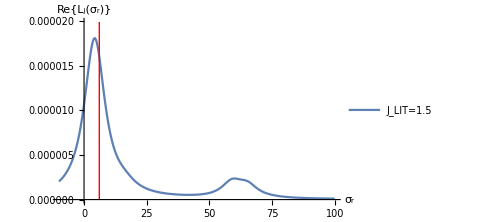
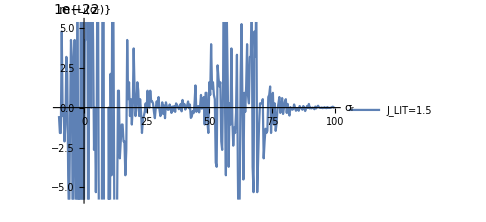
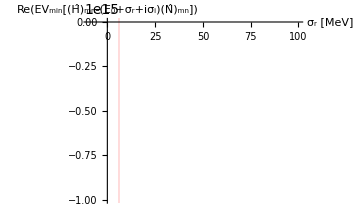
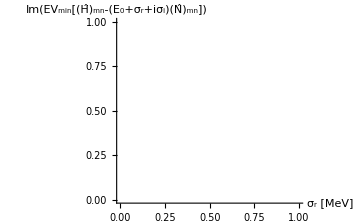
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | E_0 = -6.0933 MeV   dim_(LIT - basis) = 117

```mathematica
j0=0.5;jlit=1.5;
σI=5;
smin=-10;smax=100;nbrs=300;
σR=Range[smin,smax,(smax-smin)/(nbrs-1)];
Export[v18uixpath<>"sRange",{σI,N[σR]},"Table","FieldSeparators"->" ; "];

kR=ReadList[v18uixpath<>"kRange.dat",Real,RecordLists->True];
anzK=kR[[1]][[1]];k0=kR[[2]][[1]];dK=kR[[3]][[1]];
anzK=2;
ImLits={};ReLits={};
For[photK=1,photK≤anzK,photK++,(
kk=k0+photK dK;
Print["ω="<>ToString[kk]<>"MeV"];
Lit={};
Mats={};

For[mmj=-jlit,mmj≤jlit,mmj++,(
coflis=LofM[jlit,mmj,σR,σI,photK][[4]]//Flatten;
coflist=Transpose[{Re[coflis],Im[coflis]}];
filen=v18uixpath<>"COEFFS_LIT_J"<>ToString[jlit]<>"mJ"<>ToString[mmj];
Export[filen,coflist,"Table","FieldSeparators"->" ; "];
)];
Mats=Append[Mats,{LofM[jlit,jlit,σR,σI,photK][[2]],LofM[jlit,jlit,σR,σI,photK][[3]]}];

Ltmp= Sum[Table[LofM[jlit,m,σR,σI,photK][[1]],{m,-jlit,jlit}][[i]],{i,1,2 jlit+1}];
Lit=Append[Lit,Transpose[{σR,Ltmp}]];
ImLit=Transpose[{Re[Lit][[1]][[All,1]],Im[Lit][[1]][[All,2]]}];
ImLits=Append[ImLits,ImLit];
filen=v18uixpath<>"imag_LIT_J_"<>ToString[jlit]<>"_k_"<>ToString[kk];
Export[filen,ImLit,"Table","FieldSeparators"->" ; "];
ReLit=Transpose[{Re[Lit][[1]][[All,1]],Re[Lit][[1]][[All,2]]}];
ReLits=Append[ReLits,ReLit];
filen=v18uixpath<>"real_LIT_J_"<>ToString[jlit]<>"_k_"<>ToString[kk];
Export[filen,ReLit,"Table","FieldSeparators"->" ; "];
)]

file=v18uixpath<>"E0.dat";
EO=Read[file];Close[file];

Labeled[
Grid[{{
ListLinePlot[ReLit,
PlotLegends->Placed[{"J_LIT="<>ToString[jlit]},Above],AxesLabel->{"σ_r","Re{L_j(σ_r)}"},PlotRange->{0,1.1 Max[Re[Lit][[1]][[All,2]]]},
ImageSize->Medium,
Epilog->{Directive[{Red}],Line[{{-EO,0},{-EO,1.1 Max[Re[Lit][[1]][[All,2]]]}}]}],
ListLinePlot[ImLit,
PlotLegends->Placed[{"J_LIT="<>ToString[jlit]},Above],AxesLabel->{"σ_r","Im{L_j(σ_r)}"},
ImageSize->Medium]
},{Show[Plot[Re[LIThamDET[Mats[[1]][[2]],Mats[[1]][[1]],sr,σI,EO]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[jlit],Above],AxesLabel->{"σ_r [MeV]","Re(Det[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn])"},
ImageSize->Medium,GridLines->{{{-EO,Red}},None},PlotStyle->{colo[[0]]}]]
,Show[Plot[Im[LIThamDET[Mats[[1]][[2]],Mats[[1]][[1]],sr,σI,EO]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[jlit],Above],AxesLabel->{"σ_r [MeV]","Im(Det[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn])"},
ImageSize->Medium,GridLines->{{{-EO,Red}},None},PlotStyle->{colo[[0]]}]],Show[Plot[Abs[LIThamDET[Mats[[1]][[2]],Mats[[1]][[1]],sr,σI,EO]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[jlit],Above],AxesLabel->{"σ_r [MeV]","|Det[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn]|"},
ImageSize->Medium,PlotRange->{Automatic,{Automatic,Automatic}},GridLines->{{{-EO,Red}},None},PlotStyle->{colo[[0]]}]]
},{Show[Plot[Min[Re[LIThamEV[Mats[[1]][[2]],Mats[[1]][[1]],sr,σI,EO]]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[jlit],Above],AxesLabel->{"σ_r [MeV]","Re(EV_min[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn])"},
ImageSize->Medium,GridLines->{{{-EO,Red}},None},PlotStyle->{colo[[0]]},PlotRange->{Automatic,Automatic}]]
,
Show[Plot[Min[Im[LIThamEV[Mats[[1]][[2]],Mats[[1]][[1]],sr,σI,EO]]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[jlit],Above],AxesLabel->{"σ_r [MeV]","Im(EV_min[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn])"},
ImageSize->Medium,GridLines->{{{-EO,Red}},None},PlotStyle->{colo[[0]]},PlotRange->{Automatic,Automatic}]]
}}
],{"E_0 = "<>ToString[EO]<>" MeV   dim_(LIT - basis) = "<>ToString[Dimensions[Mats[[1]]][[2]]]},{Top}]
```

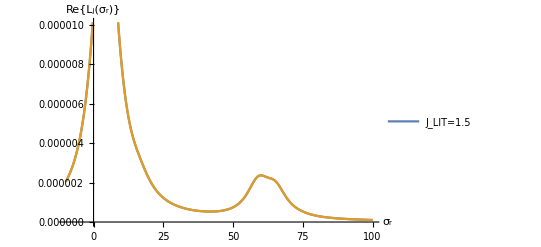

```mathematica
ListLinePlot[ReLits,
PlotLegends->Placed[{"J_LIT="<>ToString[jlit]},Above],AxesLabel->{"σ_r","Re{L_j(σ_r)}"}]
```

```mathematica
Dimensions[ReLits]
ReLits[[All,2,2]]
```

{2,300,2}

{1.06635×10^-6,1.06635×10^-6}

```mathematica
ImLit=Transpose[{Re[Lit][[1]][[All,1]],Im[Lit][[1]][[All,2]]}];
filen=v18uixpath<>"LIT_J_"<>ToString[jlit];
Export[filen,ImLit,"Table","FieldSeparators"->" ; "]; Sort
```

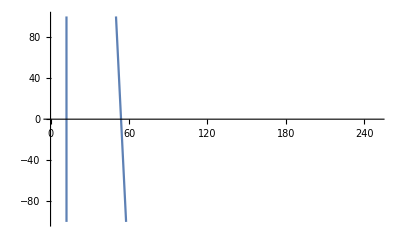

```mathematica
Plot[Sort[Re[LIThamEV[Mats[[1]][[2]],Mats[[1]][[1]],xx,σI,EO]][[1;;-1]],Smaller],{xx,smin,smax},PlotRange->{Automatic,{-100,100}}]
```